# Central Limit Theorem

A fundamental theorem in probability.

Viviana Letizia, Jun. 29,  2018

The Central Limit Theorem says that the probability distribution of the sum of n mutually independent random variables converges, as n goes to infinity, to the Normal probability distribution.

## Central Limit Theorem for Bernoulli Trials

Consider a Bernoulli trials process with probability p for success on each trial. Imagine to toss a coin showing head with probability p.

Let X_i=1 or 0 according to the ith outcome is a success or a failure and let S_n=X_1+X_2+...+X_n be the number of success on n trials. The probability distribution of S_n is the Binomial Distribution P(k)=  (n
k) (p^k(1-p))^(n-k): S_n \[Distributed]BinomialDistribution[n,p].

We plot the distributions of S_100 for different values of p: p=0.3, p=0.5, p=0.7  for 50 trials

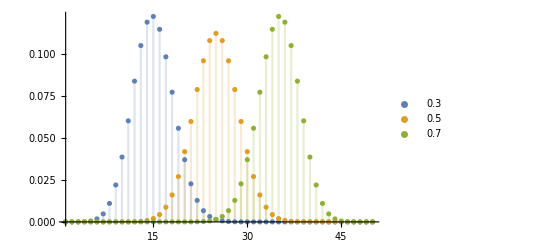

```mathematica
Table[PDF[BinomialDistribution[50,p],k],{p,{0.3,0.5,0.7}}];
DiscretePlot[Evaluate[%],{k,1,50},PlotLegends->{0.3,0.5,0.7}]
```

Remark that the maximum values of the plotted distributions appear next to the expected value np, so that they drift to the right as n increases. Moreover for n increasing, the maximum values approach 0 flattening out the spike graphs.

```mathematica
Manipulate[DiscretePlot[PDF[BinomialDistribution[n,p],k], {k, n}],{p,0,1},{n,1,100,1}]
```

## Standardized Sums

To prevent the drifting and spreading of the spike graphs we subtract the expected number of success by np, S_n-np.  We then we normalize this quantity by the standard deviation to obtain variance 1. The standardized sums are defined as follows:

S_n*= (S_n-np)/(√npq), with expected value 0 and variance 1.

We plot the standardized sum S_n* for n going from 5 to 4000 and and p = 0.3. The heights are corrected by a factor 1/ϵ, explained as follows. Since the sum of the heights of the spikes equals one, and the distance between consecutive spikes is ϵ , then the area under the curve  would be approximatively ϵ. From the definition of standardized sum then ϵ = 1/(√npq).

```mathematica
binomRescaled[n_]:=Module[{original,rescaled},
original={#,PDF[BinomialDistribution[n,0.3],#]}&/@Range[0,n];
rescaled=original;
rescaled⟦All,1⟧=(original⟦All,1⟧-n*0.3)/(√(n*0.3*0.7));
rescaled⟦All,2⟧=rescaled⟦All,2⟧/Max[rescaled⟦All,2⟧]*PDF[NormalDistribution[0,1],0];
rescaled
]
```

```mathematica
Manipulate[Show[ListPlot[Quiet[binomRescaled[n]],PlotRange->All],Plot[PDF[NormalDistribution[0,1],z],{z,-5,5}, Filling->Axis,PlotRange->All],PlotRange->{{-5,5},All}
],{n,5,4000,1}]
```

Given that the individual probabilities tend to 0 as n tends to infinity, we are rather interested in the probability that a possible outcome lies in a given interval, say [a,b]. This is equal to ask that S_n* lies between a* and b*, where a* and b* are the standardized values of a and b. As n goes to infinity the sum of these areas approach the area under the standard normal density between [a*,b*].

## Theorem

Let S_n  be the number of successes in n Bernoulli trials with probability p for success, and let a and b be two ﬁxed real numbers. Deﬁne

a* = (a-np)/(√npq)

and

b* = (b−np)/(√npq).

Then

lim n→∞ P (a ≤ S_n≤ b)= ∫_(a*)^(b^*)  φ(x)dx ,

where ϕ is the standard normal density distribution PDF[NormalDistribution[0,1],x].

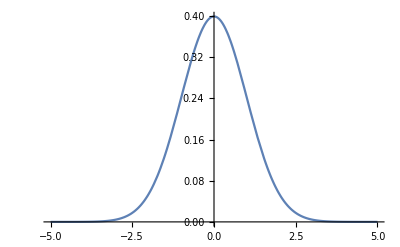

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5}]
```

#### Examples

A fair coin is tossed 100 times, we want to estimate the probability that the number of heads lies between 40 and 60. The expected number of heads is  100 1/2=50, and the standard deviation for the number of heads is √100 1/2 1/2=5. Thus, since n is already a large number, we have

P(40≤ S_n*≤60) ≈ P((39.5-50)/5≤S_n*≤ (60.5-50)/5)= P(-2.1≤Sn*≤ 2.1) ≈∫_-2.1^2.1  φ(x)dx

That is

```mathematica
Probability[-2.1≤x≤2.1,x\[Distributed]NormalDistribution[]]
```

0.964271

An application in statistics: the 95 percent conﬁdence interval for the unknown value of p. The name is suggested by the fact that if we use this method to estimate p in a large number of samples we should expect that in about 95 percent of the samples the true value of p is contained in the conﬁdence interval obtained from the sample. An estimate of p is the provided by the average value p^- = S_n/n, the proportion of successes. Given that  p^- is a linear function of S_n*, it is approximated by the normal distribution:          p^- = √ pq/n S_n*+ p . The mean of p^- is p and the standard deviation is √pq/n.  The standardized version ofp^- is p^-*= (p^--p)/(√pq/n). So we ask  P(p-2√pq/n < p^- < p+ 2√pq/n ) ≈ .95 and (p-2√pq/n , p+ 2√pq/n ) is the 95 percent confidence interval for the unknown value of p.

## Further explorations

Law of Large Numbers

Normal Distribution

## Author contact information

viviana.letizia@gmail.com